## Install and Setup

### Install Package/Application

the T3OpenInterface is build using Mathematica 9 Home Edition and jdk1.7.0_25 64-Bit:
java version “1.7.0_25”
Java(TM) SE Runtime Environment (build 1.7.0_25-b17)
Java HotSpot(TM) 64-Bit Server VM (build 23.25-b01, mixed mode)

To install T3OpenInterface use Mathematica menu :
  File/Install

You must chose ‘install for all users that share this computer’ option. This options put the package inside the $BaseDirectory of your Mathematica.

You can check the correct installation browsing the folder

```mathematica
$BaseDirectory
```

C:\ProgramData\Mathematica

### Load Package

```mathematica
Needs["T3OpenInterface`"]
```

When you load the T3OpenInterface package three thinks happen:
1. the JLink is loaded 
2. the class path is setted to $BaseDirectory, "\T3OpenInterface\Java"
3. the command ReinstallJava[CommandLine -> "E:\\Java\\jre7\\bin\\javaw.exe"] is submitted.

But if the path of your Jre7_ 64 bit is different you have su submit again the following command:
 ReinstallJava[CommandLine -> "<my_jre7_64bit_javaw.exe_path>"];

### Check Loaded Packages

You can check the installed package using the $Packages system variable :

```mathematica
$Packages
```

{JLink`,T3OpenInterface`,GetFEKernelInit`,ResourceLocator`,PacletManager`,QuantityUnits`,WebServices`,System`,Global`}

and check the exported functions/variables :

```mathematica
Names["t3*"]
```

{t3OpenFormatSearchList,t3OpenGetHDailyClosePrice,t3OpenGetMarketList,t3OpenGetStatus,t3OpenGetSubscribedData,t3OpenGetTickerByName,t3OpenObject,t3OpenSubscribe,t3OpenSubscribeBestAsk1,t3OpenSubscribeBestBid1,t3OpenSubscribeLastPrice,t3OpenUnsubscribe}

## The com.t3.t3Open java class

I've submitted the compiled class (jdk1.7.0_25 64 - bit) and source java file.

If you want to use t3Open.class on different java version you have to compile it.

```mathematica
FileNames["*",StringJoin[$BaseDirectory,"\\Applications\\T3OpenInterface\\Java\\src\\com\\t3"]]
```

{C:\ProgramData\Mathematica\Applications\T3OpenInterface\Java\src\com\t3\t3Open.java}

### Exploring com.t3.t3Open class

As Mathematica user you don't need to know about this class, but here I’m going to show you something.
If you are a good java developer you can help me to write a better and safe code.

```mathematica
Constructors["com.t3.t3Open"]
```

t3Open(String, Integer, Integer)

com.t3.t3Open has no public fileds:

```mathematica
Fields["com.t3.t3Open"]
```

{}

```mathematica
Methods["com.t3.t3Open",Inherited->False]
```

String getIpAddress()
String getPooledData()
String getPoolingWhat()
String getPoolingWhatCode()
String getPoolingWhatSymbol()
Integer getPortNumber()
java.io.BufferedReader getRefBufReader()
java.io.PrintWriter getRefOutStream()
java.net.Socket getRefSocket()
Integer getSocketTimeOut()
void getSubscribedData()
void openConnection()
void setIpAddress(String)
void setPoolingWhatCode(String)
void setPoolingWhat(String)
void setPoolingWhatSymbol(String)
void setPortNumber(Integer)
void setRefBufReader(java.io.BufferedReader)
void setRefOutStream(java.io.PrintWriter)
void setRefSocket(java.net.Socket)
void setSocketTimeOut(Integer)

## User Guide

At this point you must run nexT3OPEN.jnlp that will run T3Open from java webstart 
(see https://www.webank.it/webankpub/wb/schedaProdotto.do?tabId=nav_pub_wb_trading_nw&OBS_KEY=pro_wbn_piattaforme&KEY4=pro4_t3_open)

```mathematica
Quit[]
```

```mathematica
Needs["T3OpenInterface`"]
```

### Check T3Open Status

```mathematica
?t3OpenGetStatus
```

t3OpenGetStatus[OptionsPattern[]];
restituisce OK se lo stato della piattaforma e' valido

```mathematica
Options[t3OpenGetStatus]
```

{Private`ipAddress→127.0.0.1,Private`httpPort→8333}

```mathematica
t3OpenGetStatus[]
```

outcome=OK

### Show Markets on wihich you can Trade usin WeBank T3OPEN

```mathematica
?t3OpenGetMarketList
```

t3OpenGetMarketList[OptionsPattern[]]
restituisce la lista dei mercati su cui e' possibile operare dalla T3Open.

```mathematica
Options[t3OpenGetMarketList]
```

{Private`ipAddress→127.0.0.1,Private`httpPort→8333}

```mathematica
t3OpenGetMarketList[]
```

{{outcome=OK|numElements=21},{element=MI|EQCON},{element=MI|CW},{element=MI|MRT},{element=TLX|ELX},{element=MI|HIMTF},{element=OTC|OBOTC},{element=AK|AKIS},{element=MI|DER},{element=FR|EQXET},{element=EUR|EQPA},{element=LON|EQLSE},{element=MA|EQIBE},{element=EUR|EQAMS},{element=EUR|EQBRU},{element=EUR|EQPSI},{element=FR|EUREX},{element=EUR|LIF},{element=NY|EQNY},{element=NQ|EQNQ},{element=CME|CEQFU},{element=CME|CBOFU}}

### Show Lotti minimi

This function bypass T3Open and make a query on web

```mathematica
?borsaItalianaGetLottiMinimi
```

borsaItalianaGetLottiMinimi[];
restituisce la tabella dei lotti minimi sulle opzioni isoalpha preleva i dati dal sito di borsaitaliana.it
I lotti minimi vengono prelevati da fonte esterna e non da T3Open

```mathematica
borsaItalianaGetLottiMinimi[]
```

{{Sottostante ,Lotto minimo },{A2A ,5000 },{Acea ,500 },{Ansaldo ,500 },{Atlantia ,500 },{Autogrill ,500 },{Azimut Holding ,500 },{Banca Monte dei Paschi di Siena* ,5000 },{Banca Popolare di Milano ,5000 },{Banco Popolare ,1000 },{Banca Popolare Emilia Romagna ,1000 },{Buzzi Unicem ,100 },{Davide Campari ,1000 },{Diasorin ,500 },{Enel* ,500 },{Enel Green Power ,1000 },{Eni* ,500 },{Erg ,500 },{Exor ,100 },{Fiat* ,500 },{Fiat Industrial ,500 },{Finmeccanica ,500 },{Fondiaria-Sai ,1000 },{Generali* ,100 },{Geox ,500 },{Intesa Sanpaolo* ,1 000 },{Intesa Sanpaolo Risparmio ,1 000 },{Italcementi ,100 },{Lottomatica ,100 },{Luxottica Group ,500 },{Mediaset ,1 000 },{Mediobanca ,500 },{Mediolanum ,500 },{Mondadori ,1 000 },{Parmalat ,1 000 },{Pirelli & C. ,500 },{Prysmian ,100 },{Saipem ,500 },{Salvatore Ferragamo ,500 },{Saras ,1000 },{Snam Rete Gas ,1 000 },{Stmicroelectronics* ,500 },{Telecom Italia* ,1 000 },{Telecom Italia Risparmio ,1 000 },{Tenaris ,500 },{Terna ,5 000 },{Tod's ,100 },{Ubi Banca ,500 },{Unicredit* ,1000 },{Unipol ,500 }}

### Search For Tickers and Code

```mathematica
?t3OpenGetTickerByName
```

t3OpenGetTickerByName[exchange_,market_,pattern_,OptionsPattern[]]
restituisce il risultato di una interrogazione con pattern.
{ipAddress->'127.0.0.1',httpPort→8333}

```mathematica
Options[t3OpenGetTickerByName]
```

{Private`ipAddress→127.0.0.1,Private`httpPort→8333,Private`type→N}

We use GetTickerByName when we want know the code and the ticker symbol knowing the stock/future name:

```mathematica
t3OpenGetTickerByName["MI","EQCON","generali"]
```

outcome=OK|numElements=2
element=MI|EQCON|122721|BANCA GENERALI|BGN
element=MI|EQCON|1|GENERALI|G

```mathematica
t3OpenGetTickerByName["MI","DER","stock*future*generali"]
```

outcome=OK|numElements=6
element=MI|DER|796667|STOCK FUTURE Generali 16/08/2013|G3H
element=MI|DER|808920|STOCK FUTURE Generali 18/10/2013|G3J
element=MI|DER|803944|STOCK FUTURE Generali 20/06/2014|G4F
element=MI|DER|720730|STOCK FUTURE Generali 20/09/2013|G3I
element=MI|DER|764213|STOCK FUTURE Generali 20/12/2013|G3L
element=MI|DER|780964|STOCK FUTURE Generali 21/03/2014|G4C

```mathematica
t3OpenGetTickerByName["MI","DER","future*ftse*mib"]
```

outcome=OK|numElements=11
element=MI|DER|764428|FUTURE FTSE MIB DIVIDEND INDEX 15/12/2017|FDIV7L
element=MI|DER|668669|FUTURE FTSE MIB DIVIDEND INDEX 16/12/2016|FDIV6L
element=MI|DER|600466|FUTURE FTSE MIB DIVIDEND INDEX 18/12/2015|FDIV5L
element=MI|DER|286729|FUTURE FTSE MIB DIVIDEND INDEX 19/12/2014|FDIV4L
element=MI|DER|286730|FUTURE FTSE MIB DIVIDEND INDEX 20/12/2013|FDIV3L
element=MI|DER|803730|FUTURE FTSE MIB INDEX 20/06/2014|FIB4F
element=MI|DER|720541|FUTURE FTSE MIB INDEX 20/09/2013|FIB3I
element=MI|DER|764170|FUTURE FTSE MIB INDEX 20/12/2013|FIB3L
element=MI|DER|780774|FUTURE FTSE MIB INDEX 21/03/2014|FIB4C
element=MI|DER|780673|Mini FUTURE FTSE MIB INDEX 20/09/2013|MINI3I
element=MI|DER|803411|Mini FUTURE FTSE MIB INDEX 20/12/2013|MINI3L

Here we search for call option on FTSE MIB Italian Index:

```mathematica
t3OpenGetTickerByName["MI","DER","option*ftse*mib*09/2013*call"]
```

outcome=OK|numElements=23
element=MI|DER|724524|OPTION FTSE MIB 20/09/2013 CALL 11000|MIBO3I11000
element=MI|DER|723093|OPTION FTSE MIB 20/09/2013 CALL 11500|MIBO3I11500
element=MI|DER|722774|OPTION FTSE MIB 20/09/2013 CALL 12000|MIBO3I12000
element=MI|DER|720637|OPTION FTSE MIB 20/09/2013 CALL 12500|MIBO3I12500
element=MI|DER|720638|OPTION FTSE MIB 20/09/2013 CALL 13000|MIBO3I13000
element=MI|DER|720639|OPTION FTSE MIB 20/09/2013 CALL 13500|MIBO3I13500
element=MI|DER|720640|OPTION FTSE MIB 20/09/2013 CALL 14000|MIBO3I14000
element=MI|DER|720641|OPTION FTSE MIB 20/09/2013 CALL 14500|MIBO3I14500
element=MI|DER|720705|OPTION FTSE MIB 20/09/2013 CALL 15000|MIBO3I15000
element=MI|DER|720706|OPTION FTSE MIB 20/09/2013 CALL 15500|MIBO3I15500
element=MI|DER|720707|OPTION FTSE MIB 20/09/2013 CALL 16000|MIBO3I16000
element=MI|DER|720708|OPTION FTSE MIB 20/09/2013 CALL 16500|MIBO3I16500
element=MI|DER|720709|OPTION FTSE MIB 20/09/2013 CALL 17000|MIBO3I17000
element=MI|DER|720710|OPTION FTSE MIB 20/09/2013 CALL 17500|MIBO3I17500
element=MI|DER|720711|OPTION FTSE MIB 20/09/2013 CALL 18000|MIBO3I18000
element=MI|DER|720712|OPTION FTSE MIB 20/09/2013 CALL 18500|MIBO3I18500
element=MI|DER|720713|OPTION FTSE MIB 20/09/2013 CALL 19000|MIBO3I19000
element=MI|DER|720714|OPTION FTSE MIB 20/09/2013 CALL 19500|MIBO3I19500
element=MI|DER|724525|OPTION FTSE MIB 20/09/2013 CALL 20000|MIBO3I20000
element=MI|DER|724674|OPTION FTSE MIB 20/09/2013 CALL 20500|MIBO3I20500
element=MI|DER|763190|OPTION FTSE MIB 20/09/2013 CALL 21000|MIBO3I21000
element=MI|DER|761810|OPTION FTSE MIB 20/09/2013 CALL 21500|MIBO3I21500
element=MI|DER|766690|OPTION FTSE MIB 20/09/2013 CALL 22000|MIBO3I22000

```mathematica
?t3OpenFormatSearchList
```

formatta il risultato proveniente da t3OpenGetTickerByName

FormatSearchList remove outcome, numElements and elemnt string:

```mathematica
t3OpenFormatSearchList[t3OpenGetTickerByName["MI","DER","option*ftse*mib*09/2013*call"]]//TableForm
```

MI|DER|724524|OPTION FTSE MIB 20/09/2013 CALL 11000|MIBO3I11000
MI|DER|723093|OPTION FTSE MIB 20/09/2013 CALL 11500|MIBO3I11500
MI|DER|722774|OPTION FTSE MIB 20/09/2013 CALL 12000|MIBO3I12000
MI|DER|720637|OPTION FTSE MIB 20/09/2013 CALL 12500|MIBO3I12500
MI|DER|720638|OPTION FTSE MIB 20/09/2013 CALL 13000|MIBO3I13000
MI|DER|720639|OPTION FTSE MIB 20/09/2013 CALL 13500|MIBO3I13500
MI|DER|720640|OPTION FTSE MIB 20/09/2013 CALL 14000|MIBO3I14000
MI|DER|720641|OPTION FTSE MIB 20/09/2013 CALL 14500|MIBO3I14500
MI|DER|720705|OPTION FTSE MIB 20/09/2013 CALL 15000|MIBO3I15000
MI|DER|720706|OPTION FTSE MIB 20/09/2013 CALL 15500|MIBO3I15500
MI|DER|720707|OPTION FTSE MIB 20/09/2013 CALL 16000|MIBO3I16000
MI|DER|720708|OPTION FTSE MIB 20/09/2013 CALL 16500|MIBO3I16500
MI|DER|720709|OPTION FTSE MIB 20/09/2013 CALL 17000|MIBO3I17000
MI|DER|720710|OPTION FTSE MIB 20/09/2013 CALL 17500|MIBO3I17500
MI|DER|720711|OPTION FTSE MIB 20/09/2013 CALL 18000|MIBO3I18000
MI|DER|720712|OPTION FTSE MIB 20/09/2013 CALL 18500|MIBO3I18500
MI|DER|720713|OPTION FTSE MIB 20/09/2013 CALL 19000|MIBO3I19000
MI|DER|720714|OPTION FTSE MIB 20/09/2013 CALL 19500|MIBO3I19500
MI|DER|724525|OPTION FTSE MIB 20/09/2013 CALL 20000|MIBO3I20000
MI|DER|724674|OPTION FTSE MIB 20/09/2013 CALL 20500|MIBO3I20500
MI|DER|763190|OPTION FTSE MIB 20/09/2013 CALL 21000|MIBO3I21000
MI|DER|761810|OPTION FTSE MIB 20/09/2013 CALL 21500|MIBO3I21500
MI|DER|766690|OPTION FTSE MIB 20/09/2013 CALL 22000|MIBO3I22000

```mathematica
t3OpenFormatSearchList[t3OpenGetTickerByName["MI","EQCON","generali"]]
```

{MI|EQCON|122721|BANCA GENERALI|BGN,MI|EQCON|1|GENERALI|G}

### Submit Request on LastPrice, BestBid e BestAsk on one stock code

```mathematica
Quit[];
```

```mathematica
Needs["T3OpenInterface`"]
```

```mathematica
data = t3OpenFormatSearchList[t3OpenGetTickerByName["MI","EQCON","generali"]]
```

{MI|EQCON|122721|BANCA GENERALI|BGN,MI|EQCON|1|GENERALI|G}

We want subscribe data on Generali G, so we drop BGN:

```mathematica
generaliG=Drop[data,1]
```

{MI|EQCON|1|GENERALI|G}

t3OpenObject request the couples {{code,symbol}}, si we must manipulate generaliG:

```mathematica
generaliG = StringSplit[generaliG,"|"]
```

{{MI,EQCON,1,GENERALI,G}}

```mathematica
generaliG= Flatten[{generaliG[[All,3]],generaliG[[All,5]]}]
```

{1,G}

We want subscribe to last_price, best_bid1 and best_ask1, so we are going to create 3 t3OpenObject an we need 3 couple of {1,G}:

```mathematica
{generaliG,generaliG,generaliG}
```

{{1,G},{1,G},{1,G}}

Now we pass above structure to t3OpenObject :

```mathematica
?t3OpenObject
```

t3OpenObject[objList_,OptionsPattern[]]
crea un oggetto o lista di oggetti delle classe com.t3.T3Open ed esegue il metodo openConnection[]
che apre per ogni oggetto un socket con la piattaforma.
objList deve essere una lista di copie {{code,symbol}} precedentemente create usando t3OpneGetTickerByName.
{ipAddress->'192.168.0.78',tcpPort->5333,soTimeout→250} sono le opzioni di default

```mathematica
connectedList =t3OpenObject[{generaliG,generaliG,generaliG}]
```

{{1,G,«JavaObject[com.t3.t3Open]»},{1,G,«JavaObject[com.t3.t3Open]»},{1,G,«JavaObject[com.t3.t3Open]»}}

```mathematica
Head[connectedList[[1]][[1]]]
```

String

Now we subscribe the data source :

```mathematica
{t3OpenSubscribeLastPrice[connectedList[[1]][[3]],"MI","EQCON",connectedList[[1]][[1]]],t3OpenSubscribeBestBid1[connectedList[[2]][[3]],"MI","EQCON",connectedList[[2]][[1]]],t3OpenSubscribeBestAsk1[connectedList[[3]][[3]],"MI","EQCON",connectedList[[3]][[1]]]}
```

{outcome=OK|item=MI.EQCON.1,outcome=OK|item=MI.EQCON.1,outcome=OK|item=MI.EQCON.1}

If we want to know what we have subscribed :

```mathematica
moreConnInfo =Table[{connectedList[[All,3]][[i]]@getPoolingWhat[],connectedList[[All,3]][[i]]@getSocketTimeOut[]},{i,1,Dimensions[connectedList[[All,3]]][[1]]}]
```

{{last_price,250},{best_bid1,250},{best_ask1,250}}

We can append moreConnInfo to connectedList, so it' s simpler to know what kind of data we are pooling :

```mathematica
connectedList=Table[Append[connectedList[[i]],moreConnInfo[[i]]],{i,1,Dimensions[connectedList][[1]]}]
```

{{1,G,«JavaObject[com.t3.t3Open]»,{last_price,250}},{1,G,«JavaObject[com.t3.t3Open]»,{best_bid1,250}},{1,G,«JavaObject[com.t3.t3Open]»,{best_ask1,250}}}

Now we can refresh data :

```mathematica
refresh = {t3OpenGetSubscribedData[connectedList[[1]][[3]]],t3OpenGetSubscribedData[connectedList[[2]][[3]]],t3OpenGetSubscribedData[connectedList[[3]][[3]]]}
```

{{MI.EQCON.1|14.73},{MI.EQCON.1|14.71},{MI.EQCON.1|14.72}}

If you want to remove useless strings and convert in numbers :

```mathematica
ToExpression[Flatten[StringSplit[Flatten[refresh],"MI.EQCON.1|"]]]
```

{14.73,14.71,14.72}

We can write a naive 15 secods sampling :

```mathematica
liveData = {}
```

{}

```mathematica
For[i=1,i≤4,i++,liveData=Append[liveData,{i,DateString[],t3OpenGetSubscribedData[connectedList[[1]][[3]]],t3OpenGetSubscribedData[connectedList[[2]][[3]]],t3OpenGetSubscribedData[connectedList[[3]][[3]]]}];
Pause[15];
]
```

```mathematica
liveData//TableForm
```

1 | Wed 31 Jul 2013 15:42:33 | MI.EQCON.1|14.72 | MI.EQCON.1|14.7 | MI.EQCON.1|14.71
2 | Wed 31 Jul 2013 15:42:48 | MI.EQCON.1|14.73 | MI.EQCON.1|14.71 | MI.EQCON.1|14.72
3 | Wed 31 Jul 2013 15:43:03 | MI.EQCON.1|14.72 | MI.EQCON.1|14.72 | MI.EQCON.1|14.73
4 | Wed 31 Jul 2013 15:43:18 | MI.EQCON.1|14.71 | MI.EQCON.1|14.73 | MI.EQCON.1|14.74

Again we use Mathematica to purge useless strings :

```mathematica
liveData[[1,2]]
```

Wed 31 Jul 2013 15:42:33

```mathematica
Flatten[{StringSplit[liveData[[1,3]],"MI.EQCON.1|"],StringSplit[liveData[[1,4]],"MI.EQCON.1|"],StringSplit[liveData[[1,5]],"MI.EQCON.1|"]}]
```

{14.72,14.7,14.71}

```mathematica
Table[{liveData[[i,1]],liveData[[i,2]],Flatten[{StringSplit[liveData[[i,3]],"MI.EQCON.1|"],StringSplit[liveData[[i,4]],"MI.EQCON.1|"],
StringSplit[liveData[[i,5]],"MI.EQCON.1|"]}]},{i,1,Dimensions[liveData][[1]]}]
```

{{1,Wed 31 Jul 2013 15:42:33,{14.72,14.7,14.71}},{2,Wed 31 Jul 2013 15:42:48,{14.73,14.71,14.72}},{3,Wed 31 Jul 2013 15:43:03,{14.72,14.72,14.73}},{4,Wed 31 Jul 2013 15:43:18,{14.71,14.73,14.74}}}

Suppose that you have finished to samplig, Unsubscribe function will close the socket and destroy the java t3OpenObject :

```mathematica
t3OpenUnsubscribe[connectedList[[All,3]]]
```

{Removed[JavaObject24388798683021313],Removed[JavaObject2915971660513281],Removed[JavaObject9571775272714241]}

Java Object are been removed :

```mathematica
connectedList//TableForm
```

1 | G | Removed[JavaObject24388798683021313] | last_price
250
1 | G | Removed[JavaObject2915971660513281] | best_bid1
250
1 | G | Removed[JavaObject9571775272714241] | best_ask1
250

Manually remove useles data from connectedList :

```mathematica
Drop[connectedList,{},{3,4}]
```

{{1,G},{1,G},{1,G}}

```mathematica
Quit[]
```

### Richiesta LastPrice, BestBid e BestAsk su una Lista di codici

```mathematica
codeList01={{721316.,"TRN3I2.30"},{721317.,"TRN3I2.40"},{721318.,"TRN3I2.50"},{721319.,"TRN3I2.60"},{721320.,"TRN3I2.70"},{721321.,"TRN3I2.80"},{721322.,"TRN3I2.90"},{721323.,"TRN3I3"},{721324.,"TRN3I3.10"},{721325.,"TRN3I3.20"},{721326.,"TRN3I3.30"},{721327.,"TRN3I3.40"},{721328.,"TRN3I3.50"},{721329.,"TRN3I3.60"}}
```

{{721316.,TRN3I2.30},{721317.,TRN3I2.40},{721318.,TRN3I2.50},{721319.,TRN3I2.60},{721320.,TRN3I2.70},{721321.,TRN3I2.80},{721322.,TRN3I2.90},{721323.,TRN3I3},{721324.,TRN3I3.10},{721325.,TRN3I3.20},{721326.,TRN3I3.30},{721327.,TRN3I3.40},{721328.,TRN3I3.50},{721329.,TRN3I3.60}}

```mathematica
codeList02=Table[StringDrop[ToString[codeList01[[i,1]]],-1],{i,1,Dimensions[codeList01][[1]]}]
```

{721316,721317,721318,721319,721320,721321,721322,721323,721324,721325,721326,721327,721328,721329}

```mathematica
codeList01[[All,2]]
```

{TRN3I2.30,TRN3I2.40,TRN3I2.50,TRN3I2.60,TRN3I2.70,TRN3I2.80,TRN3I2.90,TRN3I3,TRN3I3.10,TRN3I3.20,TRN3I3.30,TRN3I3.40,TRN3I3.50,TRN3I3.60}

```mathematica
data=Transpose[{codeList02,codeList01[[All,2]]}]
```

{{721316,TRN3I2.30},{721317,TRN3I2.40},{721318,TRN3I2.50},{721319,TRN3I2.60},{721320,TRN3I2.70},{721321,TRN3I2.80},{721322,TRN3I2.90},{721323,TRN3I3},{721324,TRN3I3.10},{721325,TRN3I3.20},{721326,TRN3I3.30},{721327,TRN3I3.40},{721328,TRN3I3.50},{721329,TRN3I3.60}}

```mathematica
connectedList = t3OpenObject[data];
```

```mathematica
Table[t3OpenSubscribeLastprice[connectedList[[i,3]],"MI","DER",connectedList[[i,1]]],{i,1,Dimensions[connectedList][[1]]}];
```

```mathematica
Table[{connectedList[[i,1]],connectedList[[i,2]],t3OpenGetSubscribedData[connectedList[[i,3]]]},{i,1,Dimensions[connectedList][[1]]}]
```

{{721316,TRN3I2.30,{MI.DER.721316|0.0}},{721317,TRN3I2.40,{MI.DER.721317|0.0}},{721318,TRN3I2.50,{MI.DER.721318|0.0}},{721319,TRN3I2.60,{MI.DER.721319|0.0}},{721320,TRN3I2.70,{MI.DER.721320|0.0}},{721321,TRN3I2.80,{MI.DER.721321|0.0}},{721322,TRN3I2.90,{MI.DER.721322|0.0}},{721323,TRN3I3,{MI.DER.721323|0.0}},{721324,TRN3I3.10,{MI.DER.721324|0.0}},{721325,TRN3I3.20,{MI.DER.721325|0.0}},{721326,TRN3I3.30,{MI.DER.721326|0.042}},{721327,TRN3I3.40,{MI.DER.721327|0.0}},{721328,TRN3I3.50,{MI.DER.721328|0.0}},{721329,TRN3I3.60,{MI.DER.721329|0.0}}}

```mathematica
t3OpenUnsubscribe[connectedList[[All,3]]]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
connectedList
```

{{721316,TRN3I2.30,JLink`Objects`vm1`JavaObject19733029169659905},{721317,TRN3I2.40,JLink`Objects`vm1`JavaObject7944849344954369},{721318,TRN3I2.50,JLink`Objects`vm1`JavaObject6361250543960065},{721319,TRN3I2.60,JLink`Objects`vm1`JavaObject16097186848702465},{721320,TRN3I2.70,JLink`Objects`vm1`JavaObject5182676721991681},{721321,TRN3I2.80,JLink`Objects`vm1`JavaObject23645312228786177},{721322,TRN3I2.90,JLink`Objects`vm1`JavaObject9131695089385473},{721323,TRN3I3,JLink`Objects`vm1`JavaObject29752934988251137},{721324,TRN3I3.10,JLink`Objects`vm1`JavaObject13904754186911745},{721325,TRN3I3.20,JLink`Objects`vm1`JavaObject14426263242407937},{721326,TRN3I3.30,JLink`Objects`vm1`JavaObject24431287435526145},{721327,TRN3I3.40,JLink`Objects`vm1`JavaObject32477291967676417},{721328,TRN3I3.50,JLink`Objects`vm1`JavaObject9571517608230913},{721329,TRN3I3.60,JLink`Objects`vm1`JavaObject35946623775277057}}

### Historical Price

```mathematica
?t3OpenGetHDailyClosePrice
```

getHDailyClosePrice[market_String,exchange_String,code_String,fromDate_String,OptionsPattern[]];
get historical daily close price.

```mathematica
getT3OpenStatus[]
```

outcome=OK

```mathematica
Options[t3OpenGetHDailyClosePrice]
```

{Private`ipAddress→127.0.0.1,Private`httpPort→8333,Private`frequency→1D}

```mathematica
data =t3OpenGetHDailyClosePrice["MI","EQCON","1","20130701"]
```

{{1,20130701,13.72},{2,20130702,13.56},{3,20130703,13.53},{4,20130704,13.91},{5,20130705,13.71},{6,20130708,14.15},{7,20130709,14.25},{8,20130710,13.92},{9,20130711,13.94},{10,20130712,13.75},{11,20130715,13.96},{12,20130716,13.9},{13,20130717,14.08},{14,20130718,14.45},{15,20130719,14.43},{16,20130722,14.52},{17,20130723,14.4},{18,20130724,14.57},{19,20130725,14.55},{20,20130726,14.57},{21,20130729,14.54},{22,20130730,14.68},{23,20130731,14.81},{24,20130801,14.71},{25,20130802,14.74},{26,20130805,14.64},{27,20130806,14.73},{28,20130807,14.94},{29,20130808,15.18},{30,20130809,15.2},{31,20130812,15.16},{32,20130813,15.33},{33,20130814,15.52},{34,20130816,15.66},{35,20130819,15.42},{36,20130820,15.2},{37,20130821,15.03},{38,20130822,15.4},{39,20130823,15.39},{40,20130826,15.17}}

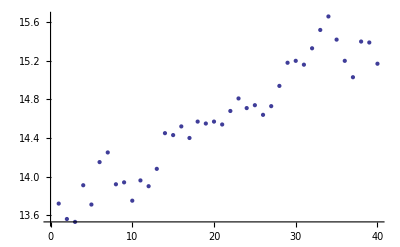

```mathematica
ListPlot[Drop[data,{},{2}]]
```

```mathematica
Options[t3OpenGetHClosePrice1M]
```

{Private`ipAddress→127.0.0.1,Private`httpPort→8333,Private`frequency→1M}

```mathematica
t3OpenGetHClosePrice1M["MI","EQCON","1","20130827"]//TableView
```

12013082709010015.0922013082709020015.0932013082709030015.0842013082709040015.0752013082709050015.1162013082709060015.172013082709070015.0882013082709080015.192013082709090015.12102013082709100015.13112013082709110015.13122013082709120015.12132013082709130015.14142013082709140015.18152013082709150015.16162013082709160015.16172013082709170015.15182013082709180015.14192013082709190015.16202013082709200015.17212013082709210015.16222013082709220015.17232013082709230015.17242013082709240015.17252013082709250015.16262013082709260015.16272013082709270015.15282013082709280015.13292013082709290015.17302013082709300015.16312013082709310015.16322013082709320015.15332013082709330015.14342013082709340015.15352013082709350015.14362013082709370015.13372013082709380015.12382013082709390015.11392013082709400015.12402013082709410015.12412013082709420015.12422013082709430015.12432013082709440015.12442013082709450015.08452013082709460015.09462013082709470015.07472013082709480015.08482013082709490015.07492013082709500015.07502013082709510015.01512013082709520014.98522013082709530014.97532013082709540014.99542013082709550014.99552013082709560015562013082709570015.02572013082709580015.02582013082709590015.03592013082710000015.03602013082710010015.03612013082710020015.01622013082710030015632013082710040014.98642013082710050014.93652013082710060014.94662013082710070014.94672013082710080014.91682013082710090014.84692013082710100014.9702013082710110014.88712013082710120014.9722013082710130014.91732013082710140014.91742013082710150014.9752013082710160014.89762013082710170014.9772013082710180014.93782013082710190014.93792013082710200014.94802013082710210014.92812013082710220014.93822013082710230014.94832013082710250014.93842013082710260014.92852013082710270014.93862013082710280014.92872013082710290014.92882013082710300014.92892013082710310014.9902013082710320014.88912013082710330014.89922013082710340014.88932013082710350014.91942013082710360014.92952013082710370014.95962013082710380014.97972013082710390014.95982013082710400014.95992013082710410014.951002013082710420014.951012013082710430014.951022013082710440014.951032013082710450014.931042013082710460014.941052013082710470014.941062013082710480014.951072013082710490014.951082013082710500014.941092013082710510014.931102013082710520014.931112013082710530014.941122013082710540014.941132013082710550014.931142013082710560014.921152013082710570014.921162013082710580014.921172013082710590014.931182013082711010014.931192013082711020014.891202013082711030014.91212013082711040014.891222013082711060014.881232013082711070014.91242013082711080014.891252013082711090014.891262013082711100014.881272013082711110014.91282013082711120014.891292013082711130014.891302013082711140014.881312013082711150014.91322013082711160014.91332013082711180014.91342013082711190014.91352013082711200014.91362013082711210014.91372013082711220014.91382013082711230014.91392013082711240014.911402013082711250014.91412013082711270014.911422013082711280014.91432013082711290014.91442013082711310014.911452013082711320014.921462013082711340014.891472013082711350014.91482013082711360014.921492013082711370014.91502013082711380014.91512013082711390014.91522013082711400014.91532013082711410014.891542013082711420014.891552013082711430014.881562013082711440014.891572013082711450014.881582013082711460014.891592013082711470014.881602013082711500014.91612013082711510014.891622013082711520014.891632013082711540014.891642013082711560014.91652013082711570014.891662013082711580014.891672013082711590014.891682013082712000014.911692013082712010014.911702013082712020014.921712013082712030014.911722013082712040014.911732013082712050014.921742013082712060014.911752013082712070014.921762013082712080014.921772013082712090014.921782013082712100014.911792013082712110014.921802013082712130014.921812013082712140014.921822013082712150014.921832013082712160014.911842013082712170014.91852013082712180014.921862013082712190014.911872013082712220014.921882013082712230014.921892013082712240014.91902013082712260014.911912013082712270014.911922013082712280014.921932013082712290014.921942013082712310014.91952013082712320014.891962013082712330014.891972013082712340014.891982013082712350014.891992013082712380014.872002013082712390014.872012013082712400014.882022013082712410014.882032013082712420014.862042013082712450014.872052013082712460014.882062013082712470014.882072013082712480014.882082013082712490014.872092013082712500014.872102013082712510014.882112013082712520014.872122013082712530014.872132013082712540014.882142013082712560014.872152013082712570014.882162013082712580014.882172013082712590014.882182013082713000014.882192013082713010014.882202013082713020014.882212013082713030014.882222013082713040014.882232013082713050014.92242013082713060014.892252013082713080014.882262013082713090014.872272013082713110014.882282013082713120014.872292013082713130014.872302013082713140014.862312013082713150014.862322013082713160014.852332013082713170014.852342013082713180014.862352013082713190014.852362013082713200014.862372013082713210014.862382013082713230014.862392013082713240014.842402013082713250014.862412013082713260014.852422013082713270014.862432013082713290014.872442013082713300014.872452013082713320014.862462013082713330014.842472013082713340014.862482013082713350014.852492013082713360014.872502013082713370014.862512013082713390014.872522013082713400014.872532013082713430014.872542013082713440014.872552013082713450014.872562013082713460014.882572013082713470014.882582013082713490014.872592013082713500014.872602013082713510014.862612013082713530014.852622013082713540014.882632013082713570014.872642013082713580014.872652013082713590014.862662013082714000014.862672013082714010014.852682013082714020014.852692013082714030014.852702013082714040014.862712013082714050014.862722013082714060014.852732013082714070014.852742013082714080014.852752013082714100014.852762013082714110014.862772013082714130014.862782013082714150014.852792013082714160014.852802013082714170014.852812013082714190014.862822013082714200014.872832013082714220014.862842013082714230014.862852013082714250014.862862013082714260014.852872013082714270014.832882013082714280014.842892013082714290014.832902013082714300014.822912013082714310014.82922013082714320014.822932013082714330014.812942013082714340014.792952013082714350014.82962013082714360014.82972013082714370014.82982013082714380014.82992013082714390014.83002013082714410014.793012013082714420014.773022013082714430014.763032013082714440014.763042013082714450014.743052013082714460014.753062013082714470014.763072013082714480014.743082013082714490014.743092013082714500014.753102013082714510014.753112013082714520014.753122013082714530014.753132013082714540014.753142013082714550014.773152013082714570014.753162013082714580014.743172013082714590014.753182013082715000014.743192013082715010014.743202013082715020014.723212013082715030014.723222013082715040014.723232013082715050014.713242013082715060014.713252013082715070014.713262013082715080014.713272013082715090014.713282013082715100014.733292013082715110014.743302013082715120014.753312013082715130014.753322013082715140014.753332013082715150014.773342013082715160014.773352013082715170014.763362013082715180014.773372013082715190014.773382013082715200014.773392013082715210014.763402013082715220014.773412013082715230014.793422013082715240014.783432013082715250014.793442013082715260014.783452013082715270014.773462013082715280014.763472013082715290014.763482013082715300014.783492013082715310014.793502013082715320014.793512013082715330014.793522013082715340014.83532013082715350014.783542013082715360014.783552013082715370014.793562013082715380014.83572013082715390014.83582013082715400014.83592013082715410014.813602013082715420014.813612013082715430014.813622013082715440014.83632013082715450014.83642013082715460014.833652013082715470014.813662013082715480014.823672013082715490014.823682013082715500014.833692013082715510014.833702013082715520014.833712013082715530014.823722013082715540014.813732013082715550014.83742013082715570014.813752013082715580014.823762013082715590014.823772013082716000014.823782013082716020014.833792013082716030014.823802013082716040014.813812013082716050014.813822013082716060014.83832013082716070014.813842013082716080014.783852013082716090014.773862013082716100014.763872013082716110014.773882013082716120014.763892013082716130014.75